## Monte Carlo Methods Case Study

I built up the theory pretty far in the last of my “Why Do They Work?” write-ups:

* https://brianhill.github.io/bayesian-statistics/resources/MonteCarloMethodsWhyDoTheyWork-III.nb.pdf

Our case study is going to be the Hepatitis B vaccination study described in Chapter 2 of Markov Chain Monte Carlo in Practice, by Gilks, Richardson, and Spiegelhalter. Gilks, Richardson, and Spiegelhalter are the editors. Chapter 2’s authors are Spiegelhalter, Best, Gilks, and Inskip.

The goal of looking closely at this case study is to see how the posterior can be practically sampled using Gibbs sampling, such as with BUGS. The BUGS reference is Gilks, Thomas, and Spiegelhalter, “A language and program for complex Bayesian modelling,” The Statistician, 43 (1994) 169-177.

## The Likelihoods and the Priors

On pp. 27 and 28 of Chapter 2, Spiegelhalter, Best, Gilks, and Inskip describe the likelihoods and the priors.

### The Likelihoods

On p. 27 the likelihoods are given in these four equations:

-Graphics-

The first two equations say that the likelihood for the y’s is:

P_y=1/(√(2π)σ)^(i·j)e^(-∑_(i,j) (y_(i,j)-α_i-β_i τ_(i,j))^2/2 σ^2)     where     τ_(i,j)≡log(t_(i,j))/730

You can certainly be forgiven if you didn’t realize that is what the first two equations say. The authors are using compact notation used by statisticians which we have not introduced in our class. The ~ means “statistically distributed according to,” and the N(μ,σ^2) means “a Gaussian with mean μ and variance σ^2,” and that is all that my equation says. Statisticians use N because they usually refer to Gaussian distributions as “normal distributions.”

I have introduced the τ_(i,j) so logarithms and the number of days in two years (365·2=730) don’t clutter my equations. It’s just a linear fit with a bit of preprocessing of the times.

The third equation says the likelihood for the α’s is:

P_α=1/(√(2π)σ_α)^i e^(-∑_i (α_i-α_0)^2/2 σ_α^2)

The fourth equation says the likelihood for the β’s is:

P_β=1/(√(2π)σ_β)^i e^(-∑_i (β_i-β_0)^2/2 σ_β^2)

### The Priors

You will notice that five new parameters have appeared in these equations: σ^2, α_0, σ_α^2, β_0 and σ_β^2. These are called “parent parameters.” We need priors for the parent parameters and on p. 28 of Chapter 2, the priors are given in these two equations.

-Graphics-

Now 10,000 is just some really big number. In fact, it is the square of 100. Let me define w=100. Then the first equation says that the priors for α_0 and β_0 are normally distributed as follows:

P_α_0=1/(√(2π)w)e^(-α_0^2/2 w^2)

P_β_0=1/(√(2π)w)e^(-β_0^2/2 w^2)

The second equation says that we should define

s=1/σ^2, s_α=1/σ_α^2, and s_β=1/σ_β^2

and then the priors for s, s_α, and s_β are Gamma distributed. Let me define v=1/w=0.01. Then:

P_s=v^v/(Γ(v))s^(v-1)e^-vs

P_s_α=v^v/(Γ(v))s_α^(v-1)e^(-v s_α)

P_s_β=v^v/(Γ(v))s_α^(v-1)e^(-v s_β)

So we have a total of five priors, one for each parameter, and the complete prior is the product of all five priors. The reason they used w=100 is that they were trying for very uninformative priors. I used w because in my mind it stood for “wide.”  The parameter v is also chosen to be uninformative (the way you make a gamma distribution very uninformative is that you choose tiny parameters.)

In fact, before we leave these priors, let me show you just how uninformative they are trying to be:

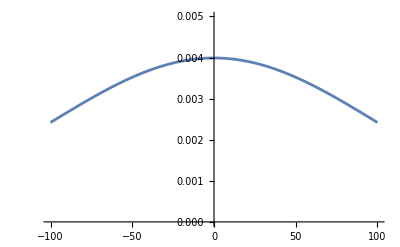

```mathematica
Plot[1/(√(2Pi) w)Exp[-Subscript[α, o]^2/(2 w^2)]/.w->100,{Subscript[α, o],-100, 100}, PlotRange->{{-100,100},{0,0.005}}]
```

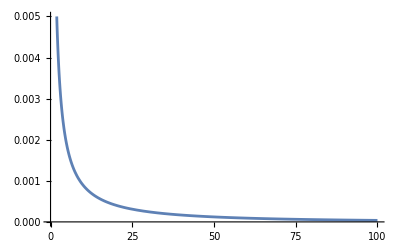

```mathematica
Plot[v^v/Gamma[v] s^(v-1)Exp[-v*s]/.v->0.01,{s,0, 100}, PlotRange->{{0,100},{0,0.005}}]
```

## The Posterior

### The Easy-to-Factor Axes

Well the posterior is the high-dimensional function we are trying to sample using Monte Carlo methods. It is the product of the three likelihood equations and the five prior equations above:

P(s,α_0,s_α,β_(0,)s_β,{α_i},{β_i})=1/(√(2π/s))^(i·j)e^(-s∑_(i,j) (y_(i,j)-α_i-β_i τ_(i,j))^2/2)·1/(√(2π/s_α))^ie^(-s_α∑_i (α_i-α_0)^2/2)·1/(√(2π/s_β))^ie^(-s_β∑_i (β_i-β_0)^2/2)·
                1/(√(2π)w)e^(-α_0^2/2 w^2)·1/(√(2π)w)e^(-β_0^2/2 w^2)·v^v/(Γ(v))s^(v-1)e^-vs·v^v/(Γ(v))s_α^(v-1)e^(-v s_α)·v^v/(Γ(v))s_β^(v-1)e^(-v s_β)

This is our function of 217 parameters. Honestly, I can’t even look at this function in its present form and see what it means. Let’s rewrite it without all the constant prefactors:

P(s,α_0,s_α,β_(0,)s_β,{α_i},{β_i})∝(√s)^(i·j)e^(-s∑_(i,j) (y_(i,j)-α_i-β_i τ_(i,j))^2/2)·(√s_α)^ie^(-s_α∑_i (α_i-α_0)^2/2)·(√s_β)^i e^(-s_β∑_i (β_i-β_0)^2/2)
              ·e^(-α_0^2/2 w^2)e^(-β_0^2/2 w^2)s^(v-1)e^-vs s_α^(v-1)e^(-v s_α)s_β^(v-1)e^(-v s_β)

Notice that in ignoring the constants, I couldn’t get rid of all the powers of the various s’s. Those are not constants. Let’s combine the powers of the various s’s up:

P(s,α_0,s_α,β_(0,)s_β,{α_i},{β_i})∝s^(v-1+i·j/2)e^(-s∑_(i,j) (y_(i,j)-α_i-β_i τ_(i,j))^2/2)·s_α^(v-1+i/2)e^(-s_α∑_i (α_i-α_0)^2/2)·s_β^(v-1+i/2)e^(-s_β∑_i (β_i-β_0)^2/2)e^(-α_0^2/2 w^2)e^(-β_0^2/2 w^2)e^-vs e^(-v s_α)e^(-v s_β)

Now it is up to us to see the way this thing factors. Rewrite:

e^(-s∑_(i,j) (y_(i,j)-α_i-β_i τ_(i,j))^2/2)=∏_i e^(-s∑_j (y_(i,j)-α_i-β_i τ_(i,j))^2/2)

And rewrite:

e^(-s_α∑_i (α_i-α_0)^2/2)=∏_i e^(-s(s_α(α_i-α_0))^2/2)

And rewrite:

e^(-s_β∑_i (β_i-β_0)^2/2)=∏_i e^(-s(s_β(β_i-β_0))^2/2)

Then

P(s,α_0,s_α,β_(0,)s_β,{α_i},{β_i})=s^(v-1+i·j/2)∏_i e^(-s∑_j (y_(i,j)-α_i-β_i τ_(i,j))^2/2)·s_α^(v-1+i/2)∏_i e^(-(s_α(α_i-α_0))^2/2)·s_β^(v-1+i/2)∏_i e^(-(s_β(β_i-β_0))^2/2)e^(-α_0^2/2 w^2)e^(-β_0^2/2 w^2)e^-vs e^(-v s_α)e^(-v s_β)

We have the factorization we required in the previous write-up:

* https://brianhill.github.io/bayesian-statistics/resources/MonteCarloMethodsWhyDoTheyWork-III.nb.pdf

The 212 α_i and β_i are indeed tangled up with the five s,α_0,s_α,β_(0,)and s_β parameters, and α_i is tangled up with β_i but α_i and β_i are factored into products that don’t involve of the 210 other α_j and β_j parameters.

That means that whenever we move in an α_i or β_i direction, we can treat as a constant multiplier the factors involving 210 of the parameters. In other words, we need only consider the tangled factors involving 7 parameters, which are:

P(s,α_0,s_α,β_(0,)s_β,α_i,β_i)∝e^(-s∑_j (y_(i,j)-α_i-β_i τ_(i,j))^2/2)·e^(-(s_α(α_i-α_0))^2/2)·e^(-(s_β(β_i-β_0))^2/2)

The products are gone, and the set symbols around α_i and β_i are gone. This might still be a somewhat complicated computation. However, thinking of the first five of these parameters as given, as we bounce around in α_i and β_i we just have exponentials of quadratic functions of α_i and β_i. In other words, we just have ordinary Gaussians. And we know how to sample ordinary Gaussians.

### The Recalcitrant Axes

Let’s look at one of the recalcitrant axes, like the first one, s. Imagining that all the other four of the recalcitrant parameters and all of the 212 α_i and β_i are fixed, we can treat everything that has no dependence on s as a constant. We are left with:

P(s,α_0,s_α,β_(0,)s_β,{α_i},{β_i})∝s^(i·j/2+v-1)e^(-s∑_(i,j) (y_(i,j)-α_i-β_i τ_(i,j))^2/2)e^-vs

Is that not just a new Gamma distribution in s? Sure, the parameters that characterize this particular Gamma distribution involve 212 other parameters and the titer data. Regardless of the formula for the parameters, we know how to sample a Gamma distribution. Remember that those other 212 parameters are just fixed numbers when we are moving along the s axis.

Let’s do one more recalcitrant axis just to see that we didn’t get lucky with the first one. How about the α_0 axis? We can treat everything with no dependence on α_0 as a constant. We are left with:

P(s,α_0,s_α,β_(0,)s_β,α_i,β_i)∝e^(-s_α∑_i (α_i-α_0)^2/2)e^(-α_0^2/2 w^2)

That’s just a Gaussian in α_0! Sure it involves 106 other parameters, but it is still a Gaussian and we know how to sample it. Remember that those other 106 parameters are fixed when we are moving along the α_0 axis.

## The Conclusion

You still have to write a lot of code to sample the posterior distribution with Gibbs sampling. Maybe that is why it took until 1994 for the BUGS program to mature and be published.

However, moving one axis at a time has for every parameter become a low-dimensional and tractable problem involving distributions we are already thoroughly familiar with.

That means we can get a representative distribution out of this 217-dimensional space using Gibbs sampling. Using these representative samples, we can inquire about the most important results from the Hepatitis B study. The parameter we are most interested in would be α_0. Remember that roughly-speaking, α_0 controls the mean of the α_i via the likelihood function,

P_α=1/(√(2π)σ_α)^i e^(-∑_i (α_i-α_0)^2/2 σ_α^2)

and the α_i represent the rate of increase of the Hepatitis B titers. We would also be interested in the variance of the α_i and that roughly speaking is in s_α=σ_α^2. However, we don’t want to know the typical values of these things in the prior. We want to know what they central values and their ranges are in the posterior.